```mathematica
Mark6 E2E Performance Results
```

## Introduction

This document describes the end to end performance results for the Mark6.

## External Libraries

```mathematica
Needs["ComputerArithmetic`"];
Needs["PlotLegends`"];
```

## Import and Process Data

```mathematica
SetDirectory["/opt/src/mark6/tests/e2e/002"];
nrFiles=FileNames["nr*.csv"]
fwFiles=FileNames["fw*.csv"]
nrData=Import[#,"CSV"]&/@nrFiles;
nrData=#[[5;;1200]]&/@nrData;
fwData=Import[#,"CSV"]&/@fwFiles;
fwData=#[[5;;1200]]&/@fwData;
numPorts=Length[nrData];
nrDataAggregate={};
For[i=1,i≤Length[nrData[[1]]],i=i+1,
AppendTo[nrDataAggregate,{nrData[[1,i,1]],Total[nrData[[All,i,5]]]}]];
Mean[nrDataAggregate[[All,2]]]
fwDataAggregate={};
For[i=1,i≤Length[fwData[[1]]],i=i+1,
AppendTo[fwDataAggregate,{fwData[[1,i,1]],Total[fwData[[All,i,5]]]}]];
Mean[fwDataAggregate[[All,2]]]
```

{nr_eth2.csv,nr_eth3.csv,nr_eth4.csv,nr_eth5.csv}

{fw_eth2.csv,fw_eth3.csv,fw_eth4.csv,fw_eth5.csv}

16228.3

16148.5

```mathematica
Per Interface Statistics
```

```mathematica
mtuSize=9000;
payloadSize=8192;
bitRate=4100000000;
numInterfaces=4;
packetRate=bitRate/(mtuSize*8);
dataRate=payloadSize*8*packetRate;
Print["per interface packetRate:",packetRate//N];
Print["per interface dataRate:",dataRate//N];
Print["total dataRate:",dataRate*numInterfaces//N];
```

per interface packetRate:56944.4

per interface dataRate:3.73191×10^9

total dataRate:1.49276×10^10

## Plot and Export

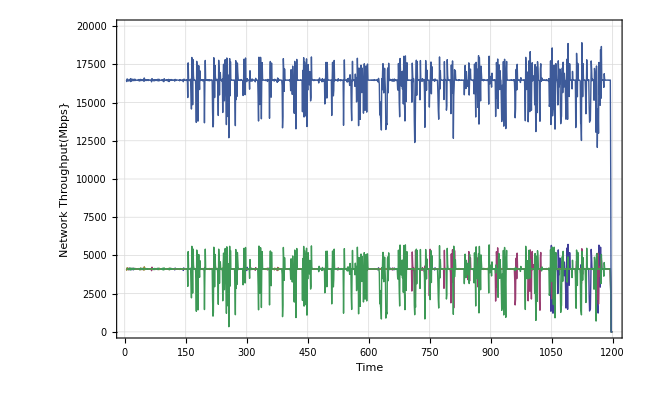

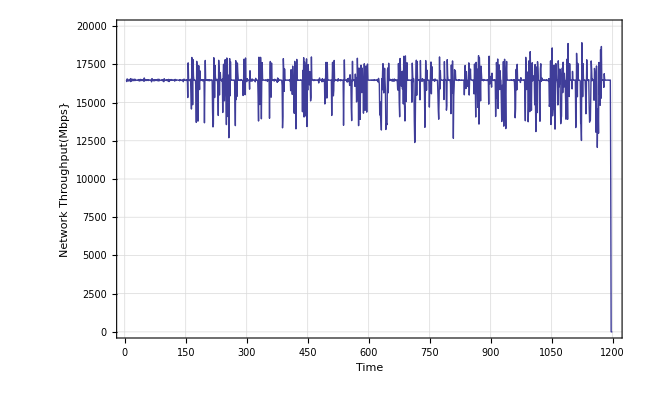

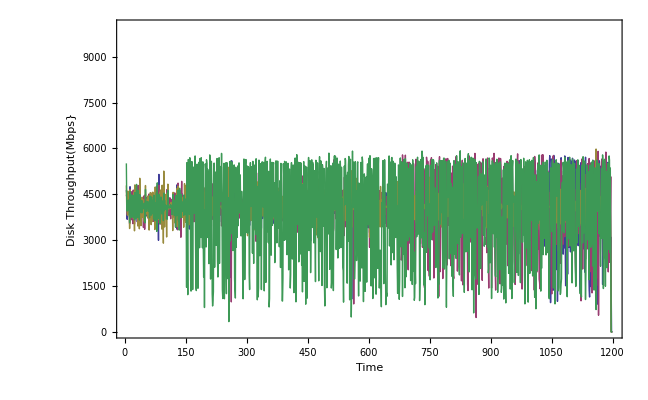

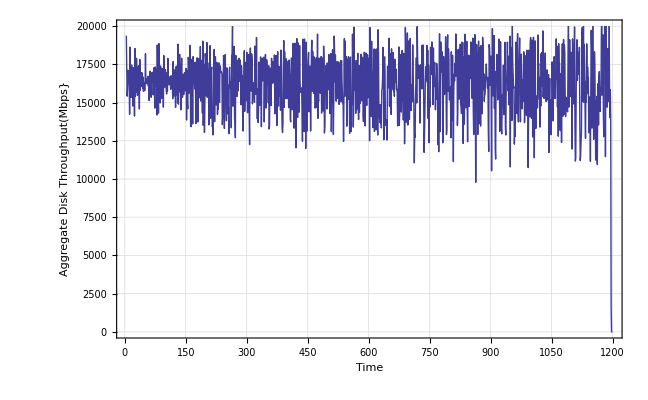

```mathematica
nrPlot=ListPlot[Append[nrData[[All,All,{1,5}]],nrDataAggregate],{Joined->True,PlotRange->{All,{0,20000}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Network Throughput(Mbps}", "E2E Network Throughput (4 x 8-Disk RAID0)",""},GridLines->Automatic ,PlotLegend->{"eth2","eth3","eth4","eth5","aggregate"},LegendShadow->False,LegendPosition->{1.1,-0.4}}]
Export["e2e_throughput.png",nrPlot];
nrAggrPlot=ListPlot[nrDataAggregate,{Joined->True,PlotRange->{All,{0,20000}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Network Throughput(Mbps}", "Aggregate Net to Mem  Throughput(4 x 10 GE @ 4 Gbps each)",""},GridLines->Automatic}]
Export["aggregate_net2mem.png",nrAggrPlot];

ListPlot[fwData[[All,All,{1,5}]],{Joined->True,PlotRange->{All,{0,10000}},ImageSize->{72  9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", "E2E Disk Throughput (4 x 8-Disk RAID0)",""}}]
fwAggrPlot=ListPlot[fwDataAggregate,{Joined->True,PlotRange->{All,{0,20000}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Aggregate Disk Throughput(Mbps}", "Aggregate Mem to Disk Throughput (4 x 8-Disk RAID0)",""},GridLines->Automatic}]
Export["aggregate_mem2disk.png",fwAggrPlot];
```

```mathematica
ListPlot[nrData[[All,All,{1,5}]],{PlotRange->{{0,60},{0,8000}},PlotJoined->True,ImageSize->{72 8, 72 6},Frame->True,PlotLegend->{"eth2","eth3","eth4","eth5"},LegendShadow->False,LegendPosition->{1.1,-0.4}},GridLines->Automatic]
```

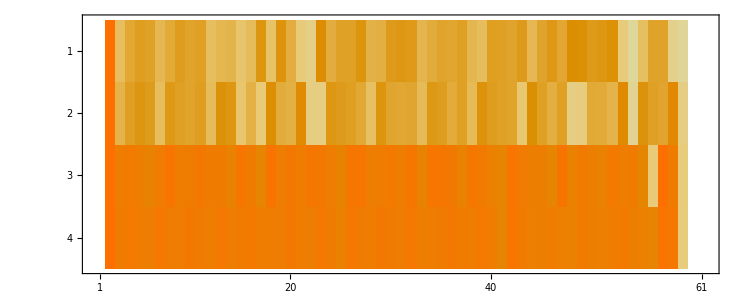

```mathematica
MatrixPlot[nrData[[All,All,5]]]
```

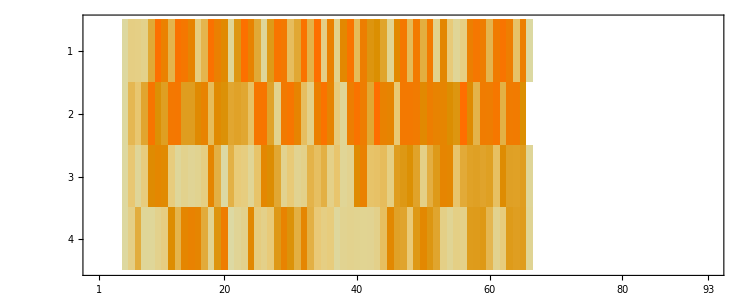

```mathematica
MatrixPlot[fwData[[All,All,5]]]
```